## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.3; qscal=0.54; Q=0.99;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.324294+1.51329×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.468509

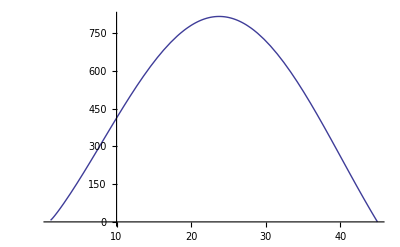

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,1.51329×10^-9},{44.8,1.55229×10^-9},{44.6,1.59241×10^-9},{44.4,1.63349×10^-9},{44.2,1.67616×10^-9},{44.,1.71985×10^-9},{43.8,1.76482×10^-9},{43.6,1.8111×10^-9},{43.4,1.86482×10^-9},{43.2,1.90883×10^-9},{43.,1.95823×10^-9},{42.8,2.01018×10^-9},{42.6,2.06364×10^-9},{42.4,2.11844×10^-9},{42.2,2.17548×10^-9},{42.,2.23388×10^-9},{41.8,2.29403×10^-9},{41.6,2.34793×10^-9},{41.4,2.41981×10^-9},{41.2,2.48555×10^-9},{41.,2.55417×10^-9},{40.8,2.62308×10^-9},{40.6,2.69501×10^-9},{40.4,2.7691×10^-9},{40.2,2.84581×10^-9},{40.,2.92421×10^-9},{39.8,3.00535×10^-9},{39.6,3.0896×10^-9},{39.4,3.17525×10^-9},{39.2,3.26319×10^-9},{39.,3.35712×10^-9},{38.8,3.45042×10^-9},{38.6,3.54794×10^-9},{38.4,3.64852×10^-9},{38.2,3.7523×10^-9},{38.,3.85931×10^-9},{37.8,3.96975×10^-9},{37.6,4.08368×10^-9},{37.4,4.20126×10^-9},{37.2,4.3226×10^-9},{37.,4.44783×10^-9},{36.8,4.57708×10^-9},{36.6,4.7105×10^-9},{36.4,4.84825×10^-9},{36.2,4.99048×10^-9},{36.,5.13773×10^-9},{35.8,5.28896×10^-9},{35.6,5.44555×10^-9},{35.4,5.60729×10^-9},{35.2,5.77423×10^-9},{35.,5.94696×10^-9},{34.8,6.12509×10^-9},{34.6,6.30933×10^-9},{34.4,6.4998×10^-9},{34.2,6.69654×10^-9},{34.,6.89964×10^-9},{33.8,7.10856×10^-9},{33.6,7.32698×10^-9},{33.4,7.55152×10^-9},{33.2,7.78381×10^-9},{33.,8.02607×10^-9},{32.8,8.27199×10^-9},{32.6,8.52356×10^-9},{32.4,8.7941×10^-9},{32.2,9.06864×10^-9},{32.,9.35267×10^-9},{31.8,9.65257×10^-9},{31.6,9.95007×10^-9},{31.4,1.0271×10^-8},{31.2,1.05903×10^-8},{31.,1.09268×10^-8},{30.8,1.12756×10^-8},{30.6,1.16359×10^-8},{30.4,1.20094×10^-8},{30.2,1.23965×10^-8},{30.,1.27963×10^-8},{29.8,1.32104×10^-8},{29.6,1.36392×10^-8},{29.4,1.40835×10^-8},{29.2,1.45435×10^-8},{29.,1.50199×10^-8},{28.8,1.55134×10^-8},{28.6,1.60242×10^-8},{28.4,1.65537×10^-8},{28.2,1.70983×10^-8},{28.,1.76702×10^-8},{27.8,1.82587×10^-8},{27.6,1.88686×10^-8},{27.4,1.95007×10^-8},{27.2,2.01556×10^-8},{27.,2.08344×10^-8},{26.8,2.15367×10^-8},{26.6,2.22657×10^-8},{26.4,2.30209×10^-8},{26.2,2.38048×10^-8},{26.,2.46157×10^-8},{25.8,2.54561×10^-8},{25.6,2.63273×10^-8},{25.4,2.7231×10^-8},{25.2,2.81671×10^-8},{25.,2.91377×10^-8},{24.8,3.0134×10^-8},{24.6,3.11865×10^-8},{24.4,3.22669×10^-8},{24.2,3.33869×10^-8},{24.,3.45478×10^-8},{23.8,3.57519×10^-8},{23.6,3.69988×10^-8},{23.4,3.82895×10^-8},{23.2,3.9627×10^-8},{23.,4.10155×10^-8},{22.8,4.24525×10^-8},{22.6,4.39409×10^-8},{22.4,4.5482×10^-8},{22.2,4.70791×10^-8},{22.,4.87363×10^-8},{21.8,5.0445×10^-8},{21.6,5.22148×10^-8},{21.4,5.40476×10^-8},{21.2,5.59437×10^-8},{21.,5.79025×10^-8},{20.8,5.99326×10^-8},{20.6,6.20244×10^-8},{20.4,6.41937×10^-8},{20.2,6.64296×10^-8},{20.,6.87381×10^-8},{19.8,7.11197×10^-8},{19.6,7.35755×10^-8},{19.4,7.61064×10^-8},{19.2,7.8712×10^-8},{19.,8.13941×10^-8},{18.8,8.41507×10^-8},{18.6,8.69831×10^-8},{18.4,8.98865×10^-8},{18.2,9.29048×10^-8},{18.,9.59053×10^-8},{17.8,9.90142×10^-8},{17.6,1.02183×10^-7},{17.4,1.05406×10^-7},{17.2,1.08676×10^-7},{17.,1.11981×10^-7},{16.8,1.15319×10^-7},{16.6,1.18659×10^-7},{16.4,1.21995×10^-7},{16.2,1.25307×10^-7},{16.,1.28561×10^-7},{15.8,1.31731×10^-7},{15.6,1.34776×10^-7},{15.4,1.37649×10^-7},{15.2,1.40291×10^-7},{15.,1.42642×10^-7},{14.8,1.44584×10^-7},{14.6,1.46037×10^-7},{14.4,1.46864×10^-7},{14.2,1.46885×10^-7},{14.,1.45902×10^-7},{13.8,1.43654×10^-7},{13.6,1.39818×10^-7},{13.4,1.33973×10^-7},{13.2,1.25593×10^-7},{13.,1.14004×10^-7},{12.8,9.83382×10^-8},{12.6,7.74885×10^-8},{12.4,5.00183×10^-8},{12.2,1.40143×10^-8},{12.,-3.299×10^-8},{11.8,-9.42341×10^-8},{11.6,-1.74264×10^-7},{11.4,-2.78351×10^-7},{11.2,-4.14684×10^-7},{11.,-5.93583×10^-7},{10.8,-8.29135×10^-7},{10.6,-1.14068×10^-6},{10.4,-1.5546×10^-6},{10.2,-2.10731×10^-6},{10.,-2.8492×10^-6},{9.8,-3.85041×10^-6},{9.6,-5.20924×10^-6},{9.4,-7.0638×10^-6},{9.2,-9.60916×10^-6},{9.,-0.0000131222},{8.8,-0.0000179972},{8.6,-0.0000247978},{8.4,-0.0000343315},{8.2,-0.0000477579},{8.,-0.0000667425},{7.8,-0.0000936767},{7.6,-0.000131986},{7.4,-0.000186556},{7.2,-0.000264305},{7.,-0.000374938},{6.8,-0.000531886},{6.6,-0.000753433},{6.4,-0.00106395},{6.2,-0.00149515},{6.,-0.00208718},{5.8,-0.00288935},{5.6,-0.00396053},{5.4,-0.00536895},{5.2,-0.00719187},{5.,-0.00951504}}

```mathematica
(*The imaginary part vs the radius*)
```

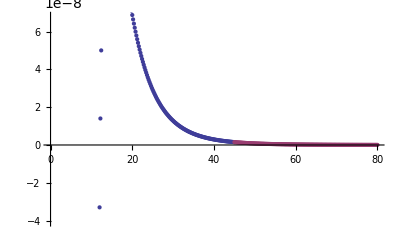

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

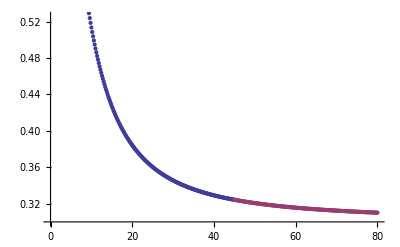

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.990/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.990/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.990/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.990/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```